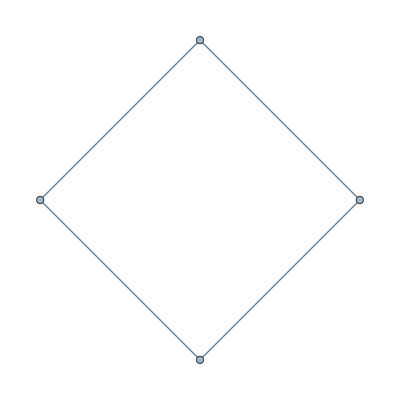

{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}}

```mathematica
g=Graph[{1<->2,2<->3,3<->4,4<->1}]
m=AdjacencyMatrix[g]//Normal
```

```mathematica
Sign[m.{-1/2,-1/2,1/2,1}]Sign[{-1/2,-1/2,1/2,1}]
```

{-1,0,1,0}

```mathematica
eps=10^-3;
RegionPlot3D[
Sign[m.{x,y,z,1}][[1]]Sign[x]>=-eps&&Sign[m.{x,y,z,1}][[2]]Sign[y]>=-eps&&Sign[m.{x,y,z,1}][[3]]Sign[z]>=-eps,
{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
FindMaximum[{Total[# Sign[#]&/@{x,y,z,w}],
AllTrue[m.{x,y,z,w}Sign[{x,y,z,w}],#>=0&],
AllTrue[{-x,y,z,w},0<=#<=1&]
},
{{x,0},{y,0},{z,0},{w,0}}]
```

{2.,{x→-1.,y→1.83252×10^-9,z→1.,w→1.83252×10^-9}}

```mathematica
a={{0,1,1},{1,0,0},{1,0,0}};
a//MatrixForm
Eigenvectors[a]
Eigenvalues[a]
```

(0 | 1 | 1
1 | 0 | 0
1 | 0 | 0)

{{-√2,1,1},{√2,1,1},{0,-1,1}}

{-√2,√2,0}

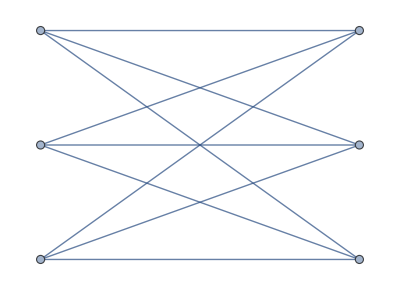

{-3.,0.,0.,0.,0.,3.}

3. | -3. | 4.44089×10^-15 | -2.22045×10^-16 | -2.37948×10^-32 | 1.3076×10^-48
{-0.408248,-0.408248,-0.408248,-0.408248,-0.408248,-0.408248} | {-0.408248,-0.408248,-0.408248,0.408248,0.408248,0.408248} | {-4.31725×10^-16,-4.31725×10^-16,-4.31725×10^-16,-0.408248,-0.408248,0.816497} | {2.57016×10^-16,2.57016×10^-16,-2.98096×10^-16,-0.707107,0.707107,0.} | {-0.408248,-0.408248,0.816497,-3.79054×10^-16,3.88578×10^-16,0.} | {0.707107,-0.707107,-9.22781×10^-17,1.16353×10^-17,-3.35156×10^-18,0.}

```mathematica
g=TuranGraph[6,2]
Eigenvalues[Normal[AdjacencyMatrix[g]]]//N//Sort
Eigensystem[Normal[AdjacencyMatrix[g]]//N]//Sort//Grid
```

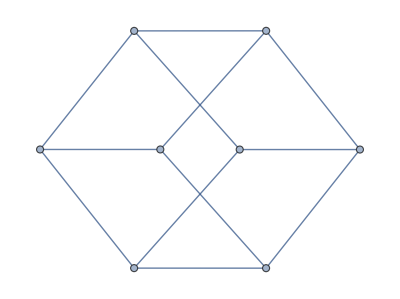

```mathematica
g=Graph[{0<->1,0<->4,0<->5,1<->2,1<->6,2<->3,2<->4,3<->6,3<->7,4<->7,5<->6,5<->7}]
```

```mathematica
Eigensystem[AdjacencyMatrix[g]]//Grid
```

-3 | 3 | -1 | -1 | -1 | 1 | 1 | 1
{1,-1,-1,-1,1,1,-1,1} | {1,1,1,1,1,1,1,1} | {0,1,0,-1,-1,0,0,1} | {1,0,0,-1,-1,0,1,0} | {0,0,1,-1,-1,1,0,0} | {0,-1,0,1,-1,0,0,1} | {-1,0,0,-1,1,0,1,0} | {0,0,-1,1,-1,1,0,0}

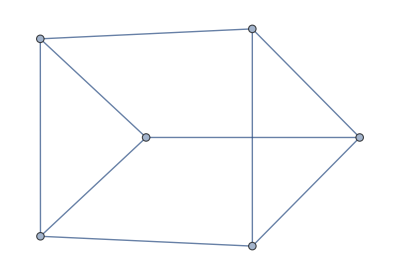

3 | -2 | -2 | 1 | 0 | 0
{1,1,1,1,1,1} | {1,0,-1,-1,0,1} | {1,-1,0,-1,1,0} | {-1,-1,-1,1,1,1} | {-1,0,1,-1,0,1} | {-1,1,0,-1,1,0}

```mathematica
g=Graph[{0<->1,1<->2,2<->0,3<->4,4<->5,5<->3,0<->3,1<->4,2<->5}]
Eigensystem[AdjacencyMatrix[g]]//Grid
```

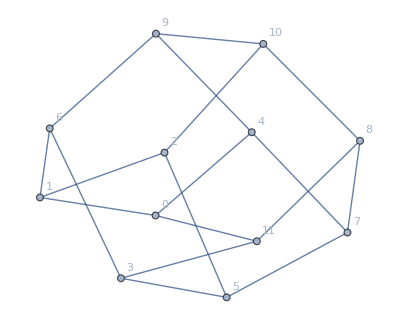

{1.56155,{-0.280776,-1.,0.280776,0.280776,-0.280776,-1.,0.280776,0.280776,-0.280776,1.,-0.280776,1.}}

```mathematica
g=Graph[{
0<->1,0<->4,0<->11,
1<->2,1<->6,
2<->5,2<->10,
3<->5,3<->6,3<->11,
4<->7,4<->9,
5<->7,
6<->9,
7<->8,
8<->10,8<->11,
9<->10
},VertexLabels->"Name"]
SortBy[Eigensystem[AdjacencyMatrix[g]]//N//Transpose,-#[[1]]&][[2]]
```

```mathematica
ContinuedFraction[GoldenRatio,5]//FromContinuedFraction
```

8/5

9

6

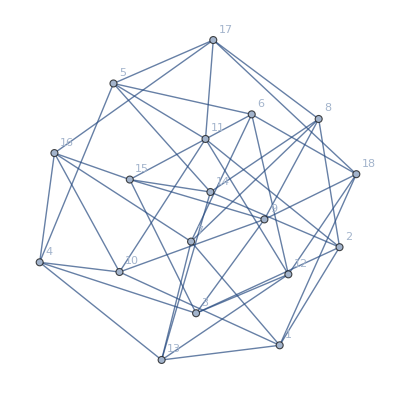

{-3.53209,-3.53209,-2.3473,-2.3473,-1.87939,-1.87939,-1.,-0.120615,-0.120615,0.347296,0.347296,1.53209,1.53209,2.,2.,2.,2.,5.}

1.5

```mathematica
p=9
step=Ceiling[p/GoldenRatio]
g=Graph[#[[1]]<->#[[2]]&/@Select[Tuples[Range[2p],{2}],(#[[1]]+1==#[[2]]||#[[1]]+p==#[[2]]||#[[1]]+step==#[[2]]||#[[1]]+step-2p==#[[2]]||#[[1]]+1-2p==#[[2]])&],
VertexLabels->"Name"]
eigs=Eigenvalues[AdjacencyMatrix[g]//N]//Sort
(eigs[[-1]]-eigs[[-2]])/2
```

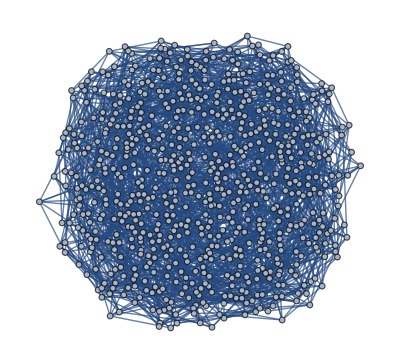

Eigenvalues::arh: Because finding 720 out of the 720 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

{-4.56155,-4.56155,-4.56155,-4.56155,-4.56155,-4.27492,-4.27492,-4.27492,-4.27492,-4.27492,-4.23827,-4.23827,-4.23827,-4.23827,-4.23827,-4.23827,-4.23827,-4.23827,-4.23827,-4.23827,-4.23827,-4.23827,-4.23827,-4.23827,-4.23827,-4.23827,-4.16737,-4.16737,-4.16737,-4.16737,-4.16737,-4.16737,-4.16737,-4.16737,-4.16737,-4.02795,-4.02795,-4.02795,-4.02795,-4.02795,-4.02795,-4.02795,-4.02795,-4.02795,-4.02795,-3.76599,-3.76599,-3.76599,-3.76599,-3.76599,-3.76599,-3.76599,-3.76599,-3.76599,-3.76599,-3.76599,-3.76599,-3.76599,-3.76599,-3.76599,-3.76599,-3.75199,-3.75199,-3.75199,-3.75199,-3.75199,-3.75199,-3.75199,-3.75199,-3.75199,-3.56155,-3.56155,-3.56155,-3.56155,-3.56155,-3.30916,-3.30916,-3.30916,-3.30916,-3.30916,-3.30916,-3.30916,-3.30916,-3.30916,-3.30916,-3.30916,-3.30916,-3.30916,-3.30916,-3.30916,-3.30916,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-2.87944,-2.87944,-2.87944,-2.87944,-2.87944,-2.87944,-2.87944,-2.87944,-2.87944,-2.87944,-2.73952,-2.73952,-2.73952,-2.73952,-2.73952,-2.73952,-2.73952,-2.73952,-2.73952,-2.73859,-2.73859,-2.73859,-2.73859,-2.73859,-2.73859,-2.73859,-2.73859,-2.73859,-2.73859,-2.73859,-2.73859,-2.73859,-2.73859,-2.73859,-2.73859,-2.69833,-2.69833,-2.69833,-2.69833,-2.69833,-2.69833,-2.69833,-2.69833,-2.69833,-2.69833,-2.69833,-2.69833,-2.69833,-2.69833,-2.69833,-2.69833,-2.63934,-2.63934,-2.63934,-2.63934,-2.63934,-2.63934,-2.63934,-2.63934,-2.63934,-2.63934,-2.4639,-2.4639,-2.4639,-2.4639,-2.4639,-2.4639,-2.4639,-2.4639,-2.4639,-2.44661,-2.44661,-2.44661,-2.44661,-2.44661,-2.44661,-2.44661,-2.44661,-2.44661,-2.44661,-2.41421,-2.41421,-2.41421,-2.41421,-2.41421,-2.41421,-2.41421,-2.41421,-2.41421,-1.91882,-1.91882,-1.91882,-1.91882,-1.91882,-1.91882,-1.91882,-1.91882,-1.91882,-1.91882,-1.91882,-1.91882,-1.91882,-1.91882,-1.91882,-1.91882,-1.79859,-1.79859,-1.79859,-1.79859,-1.79859,-1.71496,-1.71496,-1.71496,-1.71496,-1.71496,-1.71496,-1.71496,-1.71496,-1.71496,-1.71496,-1.71092,-1.71092,-1.71092,-1.71092,-1.71092,-1.71092,-1.71092,-1.71092,-1.71092,-1.71092,-1.71092,-1.71092,-1.71092,-1.71092,-1.71092,-1.71092,-1.29853,-1.29853,-1.29853,-1.29853,-1.29853,-1.29853,-1.29853,-1.29853,-1.29853,-1.29853,-1.29853,-1.29853,-1.29853,-1.29853,-1.29853,-1.29853,-1.19423,-1.19423,-1.19423,-1.19423,-1.19423,-1.19423,-1.19423,-1.19423,-1.19423,-1.19423,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-0.837003,-0.837003,-0.837003,-0.837003,-0.837003,-0.837003,-0.837003,-0.837003,-0.837003,-0.837003,-0.700916,-0.700916,-0.700916,-0.700916,-0.700916,-0.700916,-0.700916,-0.700916,-0.700916,-0.479359,-0.479359,-0.479359,-0.479359,-0.479359,-0.479359,-0.479359,-0.479359,-0.479359,-0.479359,-0.479359,-0.479359,-0.479359,-0.479359,-0.479359,-0.479359,-0.438447,-0.438447,-0.438447,-0.438447,-0.438447,-0.373113,-0.373113,-0.373113,-0.373113,-0.373113,-0.373113,-0.373113,-0.373113,-0.373113,-0.251441,-0.251441,-0.251441,-0.251441,-0.251441,-0.251441,-0.251441,-0.251441,-0.251441,-0.251441,-0.236068,-0.236068,-0.236068,-0.236068,-0.236068,-0.219265,-0.219265,-0.219265,-0.219265,-0.219265,-0.219265,-0.219265,-0.219265,-0.219265,-0.145541,-0.145541,-0.145541,-0.145541,-0.145541,-0.145541,-0.145541,-0.145541,-0.145541,-0.145541,-0.024518,-0.024518,-0.024518,-0.024518,-0.024518,-0.024518,-0.024518,-0.024518,-0.024518,-0.024518,-0.024518,-0.024518,-0.024518,-0.024518,-0.024518,-0.024518,0.149109,0.149109,0.149109,0.149109,0.149109,0.149109,0.149109,0.149109,0.149109,0.149109,0.231164,0.231164,0.231164,0.231164,0.231164,0.231164,0.231164,0.231164,0.231164,0.231164,0.231164,0.231164,0.231164,0.231164,0.231164,0.231164,0.414214,0.414214,0.414214,0.414214,0.414214,0.414214,0.414214,0.414214,0.414214,0.459563,0.459563,0.459563,0.459563,0.459563,0.459563,0.459563,0.459563,0.459563,0.561553,0.561553,0.561553,0.561553,0.561553,0.614932,0.614932,0.614932,0.614932,0.614932,0.614932,0.614932,0.614932,0.614932,0.614932,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.15949,1.15949,1.15949,1.15949,1.15949,1.15949,1.15949,1.15949,1.15949,1.15949,1.15949,1.15949,1.15949,1.15949,1.15949,1.15949,1.27447,1.27447,1.27447,1.27447,1.27447,1.27447,1.27447,1.27447,1.27447,1.31907,1.31907,1.31907,1.31907,1.31907,1.44969,1.44969,1.44969,1.44969,1.44969,1.44969,1.44969,1.44969,1.44969,1.5438,1.5438,1.5438,1.5438,1.5438,1.5438,1.5438,1.5438,1.5438,1.5438,1.62508,1.62508,1.62508,1.62508,1.62508,1.62508,1.62508,1.62508,1.62508,1.62508,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.15068,2.15068,2.15068,2.15068,2.15068,2.15068,2.15068,2.15068,2.15068,2.29626,2.29626,2.29626,2.29626,2.29626,2.29626,2.29626,2.29626,2.29626,2.29626,2.29626,2.29626,2.29626,2.29626,2.29626,2.29626,2.32381,2.32381,2.32381,2.32381,2.32381,2.32381,2.32381,2.32381,2.32381,2.32381,2.32381,2.32381,2.32381,2.32381,2.32381,2.32381,2.59137,2.59137,2.59137,2.59137,2.59137,2.59137,2.59137,2.59137,2.59137,2.59137,3.09264,3.09264,3.09264,3.09264,3.09264,3.09264,3.09264,3.09264,3.09264,3.09264,3.27492,3.27492,3.27492,3.27492,3.27492,3.37461,3.37461,3.37461,3.37461,3.37461,3.37461,3.37461,3.37461,3.37461,3.37461,3.82343,3.82343,3.82343,3.82343,3.82343,3.82343,3.82343,3.82343,3.82343,3.82343,3.82343,3.82343,3.82343,3.82343,3.82343,3.82343,3.83816,3.83816,3.83816,3.83816,3.83816,3.83816,3.83816,3.83816,3.83816,4.23607,4.23607,4.23607,4.23607,4.23607,4.2435,4.2435,4.2435,4.2435,4.2435,4.2435,4.2435,4.2435,4.2435,4.25677,4.25677,4.25677,4.25677,4.25677,4.25677,4.25677,4.25677,4.25677,4.25677,4.34833,4.34833,4.34833,4.34833,4.34833,4.34833,4.34833,4.34833,4.34833,4.34833,4.34833,4.34833,4.34833,4.34833,4.34833,4.34833,4.57012,4.57012,4.57012,4.57012,4.57012,4.57012,4.57012,4.57012,4.57012,4.57012,5.,5.,5.,5.,5.,5.31808,5.31808,5.31808,5.31808,5.31808,5.31808,5.31808,5.31808,5.31808,5.31808,5.47952,5.47952,5.47952,5.47952,5.47952,7.}

0.760241

```mathematica
n=6;
g=CayleyGraph[PermutationGroup[{Cycles[{Range[n]}],Cycles[{{1,2}}],Cycles[{{2,3,4}}],Cycles[{{4,5,6}}]}]]//UndirectedGraph
eigs=Eigenvalues[AdjacencyMatrix[g]//N]//Sort
(eigs[[-1]]-eigs[[-2]])/2
```

```mathematica
Sqrt[12]//N
```

3.4641